```mathematica
data = {{0.000000,-5},{0.129032,-4},{0.200000,-3},{0.232258,-2},{0.245161,-1},{0.258065,0},{0.290323,1},{0.361290,2},{0.490323,3},{0.696774,4},{1.000000,5}}
```

{{0.,-5},{0.129032,-4},{0.2,-3},{0.232258,-2},{0.245161,-1},{0.258065,0},{0.290323,1},{0.36129,2},{0.490323,3},{0.696774,4},{1.,5}}

```mathematica
Transpose@data
```

{{0.,0.129032,0.2,0.232258,0.245161,0.258065,0.290323,0.36129,0.490323,0.696774,1.},{-5,-4,-3,-2,-1,0,1,2,3,4,5}}

```mathematica
n=Length@data
```

11

```mathematica
{xx,yy}=Transpose@data;
Sum[Product[(x-xx[[i]])/(-xx[[i]]+xx[[j]]),{i,Complement[Range[n],{j}]}]yy[[j]],{j,n}]
```

0.-367942. (-1.+x) (-0.696774+x) (-0.490323+x) (-0.36129+x) (-0.290323+x) (-0.258065+x) (-0.245161+x) (-0.232258+x) (-0.2+x) (-0.129032+x)+4.21967×10^7 (-1.+x) (-0.696774+x) (-0.490323+x) (-0.36129+x) (-0.290323+x) (-0.258065+x) (-0.245161+x) (-0.232258+x) (-0.2+x) (0.+x)-1.48654×10^9 (-1.+x) (-0.696774+x) (-0.490323+x) (-0.36129+x) (-0.290323+x) (-0.258065+x) (-0.245161+x) (-0.232258+x) (-0.129032+x) (0.+x)+1.12628×10^10 (-1.+x) (-0.696774+x) (-0.490323+x) (-0.36129+x) (-0.290323+x) (-0.258065+x) (-0.245161+x) (-0.2+x) (-0.129032+x) (0.+x)-1.06572×10^10 (-1.+x) (-0.696774+x) (-0.490323+x) (-0.36129+x) (-0.290323+x) (-0.258065+x) (-0.232258+x) (-0.2+x) (-0.129032+x) (0.+x)+6.827×10^8 (-1.+x) (-0.696774+x) (-0.490323+x) (-0.36129+x) (-0.258065+x) (-0.245161+x) (-0.232258+x) (-0.2+x) (-0.129032+x) (0.+x)-4.869×10^7 (-1.+x) (-0.696774+x) (-0.490323+x) (-0.290323+x) (-0.258065+x) (-0.245161+x) (-0.232258+x) (-0.2+x) (-0.129032+x) (0.+x)+1.46186×10^6 (-1.+x) (-0.696774+x) (-0.36129+x) (-0.290323+x) (-0.258065+x) (-0.245161+x) (-0.232258+x) (-0.2+x) (-0.129032+x) (0.+x)-25909. (-1.+x) (-0.490323+x) (-0.36129+x) (-0.290323+x) (-0.258065+x) (-0.245161+x) (-0.232258+x) (-0.2+x) (-0.129032+x) (0.+x)+238.241 (-0.696774+x) (-0.490323+x) (-0.36129+x) (-0.290323+x) (-0.258065+x) (-0.245161+x) (-0.232258+x) (-0.2+x) (-0.129032+x) (0.+x)

```mathematica
Simplify[%22]
```

-5.-1679.41 x+1306.6 x^2+718484. x^3-1.10573×10^7 x^4+7.72642×10^7 x^5-3.02904×10^8 x^6+7.02522×10^8 x^7-9.5024×10^8 x^8+6.87295×10^8 x^9-2.03597×10^8 x^10

```mathematica
Plot[-4.999999999999999-1679.414511925006 x+1306.604336498538 x^2+718483.6883936822 x^3-1.105725778954862*^7 x^4+7.726415880698961*^7 x^5-3.0290437269082403*^8 x^6+7.025218443357706*^8 x^7-9.502404621130562*^8 x^8+6.872949719494734*^8 x^9-2.0359698337702453*^8 x^10,{x,0,1}]
```

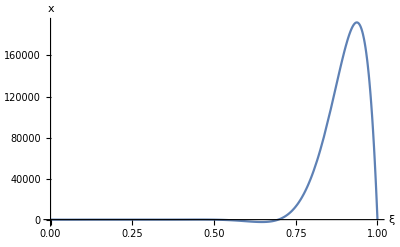

```mathematica
Show[%3,AxesLabel->{HoldForm[ξ],HoldForm[x]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```